```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
α = 0.3;C0=0.8;T=40; θ1=30;θ2=30;
case=3;
case=2;
Switch[case,
1,T=100;C0=1;C1=0.4;prefix="Fig3a_";,
2,T=100;C0=1;C1=0.5;prefix="Fig3b_";,
3,T=30;C0=1;C1=0.7;prefix="Fig3c_";,(*τ2=0.4;τ1=τ2-δ;τ3=1-δ;*)
4,T=30;C0=1;C1=0.5;prefix="Fig3d_";

]
point=1;
Switch[case,
1,T=30;C0=1;C1=0.7;τ2=0.4;δ=0.05;τ1=0.25;τ3=0.75;filename=prefix<>"";,
2,T=30;C0=1;C1=0.7;τ2=0.4;δ=0.05;τ1=0.25;τ3=0.95;filename="Fig2a_example2.png";,
3,T=30;C0=1;C1=0.7;τ2=0.4;δ=0.05;τ1=0.35;τ3=0.95;filename="Fig2a_example3.png";,
4,T=30;C0=1;C1=0.5;τ2=0.4;δ=0.05;τ1=0.25;τ3=0.75;filename="Fig2b_example1.png";,
5,T=30;C0=1;C1=0.5;τ2=0.4;δ=0.05;τ1=0.25;τ3=0.95;filename="Fig2b_example2.png";,
6,T=30;C0=1;C1=0.5;τ2=0.4;δ=0.05;τ1=0.35;τ3=0.95;filename="Fig2b_example3.png";,
7,T=100;C0=1;C1=0.4;τ2=0.4;δ=0.05;τ1=0.25;τ3=0.75;filename="Fig2c_example1.png";,
8,T=100;C0=1;C1=0.4;τ2=0.4;δ=0.05;τ1=0.25;τ3=0.95;filename="Fig2c_example2.png";,
9,T=100;C0=1;C1=0.4;τ2=0.4;δ=0.05;τ1=0.35;τ3=0.95;filename="Fig2c_example3.png"
]

(*FHN Parameters*)
ep=0.08;β=0.65;γ=0.7;maxtime=300;
Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(Mod[t,T]-τ1 T)(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T]-τ3 T)(C0-C1)/(T- τ3 T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,0, True,(C0-C1)/(T- τ3 T)];
(*Look for stable equilibrium*)
eqn=FindRoot[0==v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
```

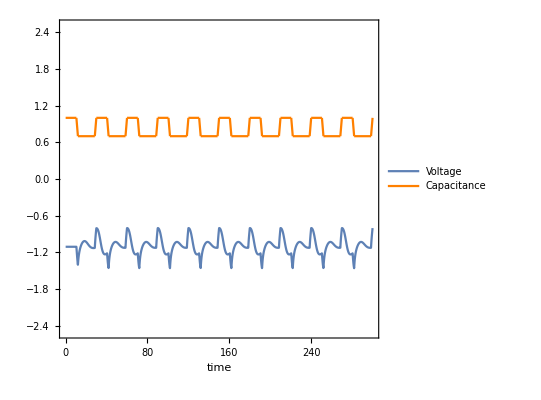

Fig2a_example3.png

```mathematica
{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0,w[0]==w0},{v,w},{t,0,maxtime},MaxStepSize->0.2Min[τ2-τ1,1-τ3]T];
(*Voltage/capacitance plot*)
voltage=Plot[V[t],{t,0,maxtime},
PlotRange->{-2.5,2.5},
TicksStyle->Directive[FontSize->16],
Frame->True,
FrameLabel->{{None,None},{"time",None}},
LabelStyle->Directive[Black,FontSize->16]
];
(*,ColorFunction->Function[{t},Which[Mod[t,2T]<T,Red,True,Default]],ColorFunctionScaling->False];*)(*,PlotLegends->Placed[StringJoin["C0=",ToString[C0],", C1=",ToString[C1],", T= ",ToString[T],",\n","τ1= ",ToString[τ1],", τ2= ",ToString[τ2],", τ3= ",ToString[τ3],",\n","ε=",ToString[ep],", γ=",ToString[γ],", β=",ToString[β]],Above]];*)
capacitance=Plot[{Ct[t]},{t,0,maxtime},
PlotPoints->10000,
MaxRecursion->3,
PlotStyle->Orange
];

g1=Legended[Show[voltage, capacitance,AspectRatio->1],Placed[LineLegend[{ColorData[97,"ColorList"][[1]],Orange},{Style["Voltage",FontSize->18],Style["Capacitance",FontSize->18]}],{{0.7,0.9}}]]
Export[filename,g1]
```